```mathematica
Needs["PlotLegends`"]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]]
Parameters=Import["Parameters"]

fy1=1;
fy2=2;
fy3=3;
fy4=4;

IntactPF=Import["Intact/PartitionFunction_0_0.out","Table"];
IntactFE=Import["Intact/FreeEnergy_0_0.out","Table"];
IntactdFE=Import["Intact/dFreeEnergy_0_0.out","Table"];

FrayedPF1=Import["Frayed/PartitionFunction_0_"<>ToString[fy1]<>".out","Table"];
FrayedFE1=Import["Frayed/FreeEnergy_0_"<>ToString[fy1]<>".out","Table"];
FrayeddFE1=Import["Frayed/dFreeEnergy_0_"<>ToString[fy1]<>".out","Table"];

FrayedPF2=Import["Frayed/PartitionFunction_0_"<>ToString[fy2]<>".out","Table"];
FrayedFE2=Import["Frayed/FreeEnergy_0_"<>ToString[fy2]<>".out","Table"];
FrayeddFE2=Import["Frayed/dFreeEnergy_0_"<>ToString[fy2]<>".out","Table"];

FrayedPF3=Import["Frayed/PartitionFunction_0_"<>ToString[fy3]<>".out","Table"];
FrayedFE3=Import["Frayed/FreeEnergy_0_"<>ToString[fy3]<>".out","Table"];
FrayeddFE3=Import["Frayed/dFreeEnergy_0_"<>ToString[fy3]<>".out","Table"];

FrayedPF4=Import["Frayed/PartitionFunction_0_"<>ToString[fy4]<>".out","Table"];
FrayedFE4=Import["Frayed/FreeEnergy_0_"<>ToString[fy4]<>".out","Table"];
FrayeddFE4=Import["Frayed/dFreeEnergy_0_"<>ToString[fy4]<>".out","Table"];

BubblePF31=Import["Bubble/PartitionFunction_3_1.out","Table"];
BubbleFE31=Import["Bubble/FreeEnergy_3_1.out","Table"];
BubbledFE31=Import["Bubble/dFreeEnergy_3_1.out","Table"];

BubblePF21=Import["Bubble/PartitionFunction_2_1.out","Table"];
BubbleFE21=Import["Bubble/FreeEnergy_2_1.out","Table"];
BubbledFE21=Import["Bubble/dFreeEnergy_2_1.out","Table"];

BubblePF22=Import["Bubble/PartitionFunction_2_2.out","Table"];
BubbleFE22=Import["Bubble/FreeEnergy_2_2.out","Table"];
BubbledFE22=Import["Bubble/dFreeEnergy_2_2.out","Table"];

BubblePF13=Import["Bubble/PartitionFunction_1_3.out","Table"];
BubbleFE13=Import["Bubble/FreeEnergy_1_3.out","Table"];
BubbledFE13=Import["Bubble/dFreeEnergy_1_3.out","Table"];
```

/Users/htailor/Desktop/code/dna/Nucleation_5/results

{{},{L:,20.},{m:,40},{N:,5},{eta_b:,1.25},{kappa_sigma_r:,1.},{Delta:,0.2469},{},{Extension Minimum:,0},{Extension Maximum:,25},{TOLERANCE:,0.}}

## Numerical Results

### Frayed - Partition Function and Free Energy

```mathematica
fsTitle=24;
fsAxesLabel=18;
fs2=16;

pIntact=ListLinePlot[IntactFE,PlotStyle->{Thick,Dashed,Darker[ColorData[1,1]]}];
pFrayedFE1=ListLinePlot[FrayedFE1,PlotStyle->{Thick,Red}];
pFrayedFE2=ListLinePlot[FrayedFE2,PlotStyle->{Thick,Orange}];
pFrayedFE3=ListLinePlot[FrayedFE3,PlotStyle->{Thick,Purple}];
pFrayedFE4=ListLinePlot[FrayedFE4,PlotStyle->{Thick,Darker[Green]}];

pdIntact=ListLinePlot[IntactdFE,PlotStyle->{Thick,Dashed,Darker[ColorData[1,1]]}];
pdFrayedFE1=ListLinePlot[FrayeddFE1,PlotStyle->{Thick,Red}];
pdFrayedFE2=ListLinePlot[FrayeddFE2,PlotStyle->{Thick,Orange}];
pdFrayedFE3=ListLinePlot[FrayeddFE3,PlotStyle->{Thick,Purple}];
pdFrayedFE4=ListLinePlot[FrayeddFE4,PlotStyle->{Thick,Darker[Green]}];


legend={{Graphics[{Thick,Dashed,Darker[ColorData[1,1]],Line[{{0,0},{2,0}}]}],Style["Intact",FontSize->fs2]},{Graphics[{Thick,Red,Line[{{0,0},{2,0}}]}],Style["Frayed "<>ToString[fy1],FontSize->fs2]},
{Graphics[{Thick,Orange,Line[{{0,0},{2,0}}]}],Style["Frayed "<>ToString[fy2],FontSize->fs2]},
{Graphics[{Thick,Purple,Line[{{0,0},{2,0}}]}],Style["Frayed "<>ToString[fy3],FontSize->fs2]},
{Graphics[{Thick,Darker[Green],Line[{{0,0},{2,0}}]}],Style["Frayed "<>ToString[fy4],FontSize->fs2]}
};

ShowLegend[
Show[{pIntact,pFrayedFE1,pFrayedFE2,pFrayedFE3,pFrayedFE4},ImageSize->Large,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["F(u)",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2}],
{legend,LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->{0.4,0.4},LegendPosition->{-0.8,0.05}}
]

ShowLegend[
Show[{pdIntact,pdFrayedFE1,pdFrayedFE2,pdFrayedFE3,pdFrayedFE4},ImageSize->{900,600},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["dF(u)/du",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2}],
{legend,LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->{0.4,0.4},LegendPosition->{-0.8,0.05}}
]
```

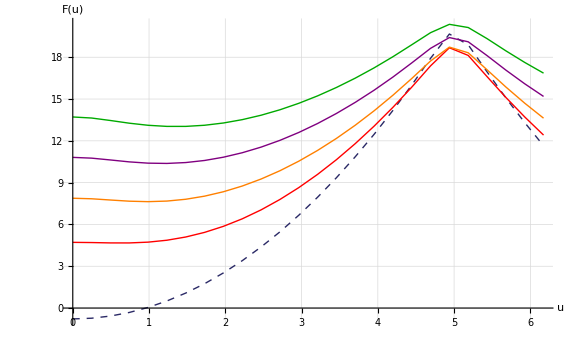

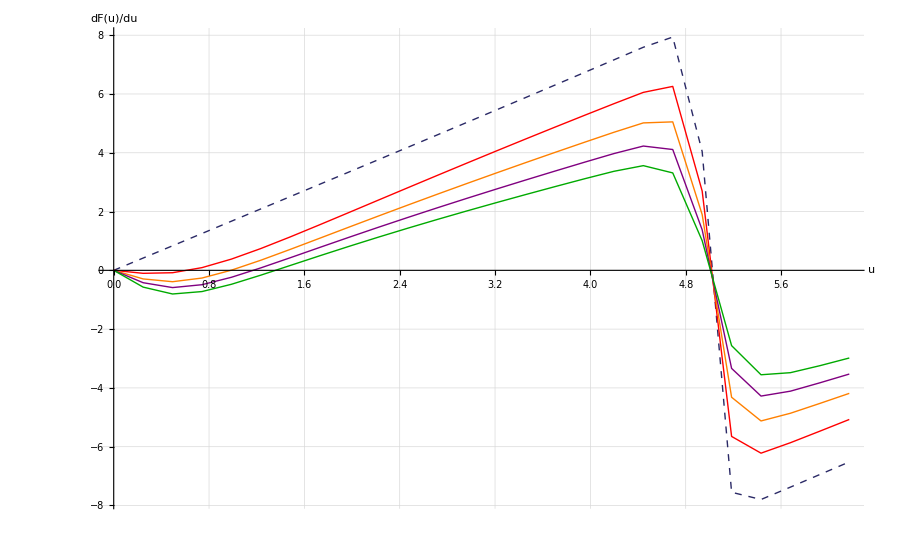

-Graphics-

### Bubbled - Partition Function and Free Energy

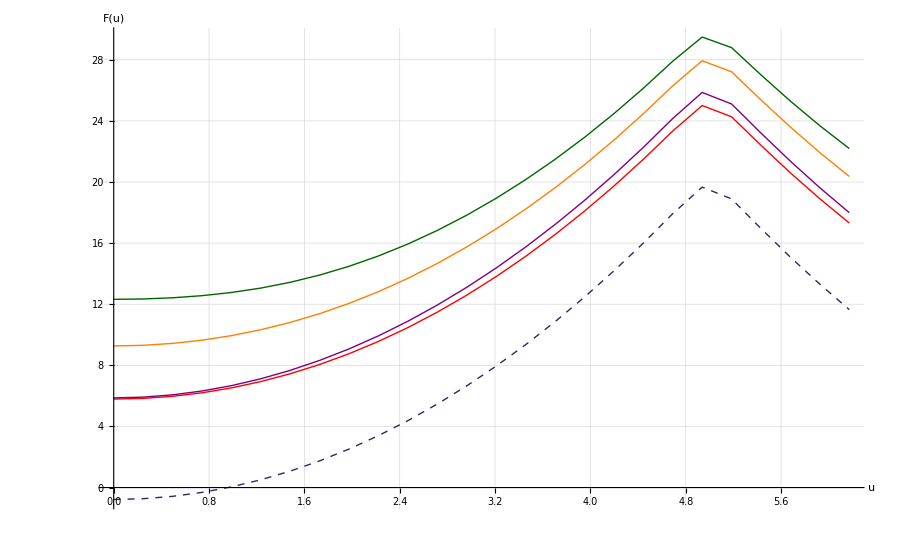

```mathematica
fsTitle=24;
fsAxesLabel=18;
fs2=16;

pIntact=ListLinePlot[IntactFE,PlotStyle->{Thick,Dashed,Darker[ColorData[1,1]]}];
pBubbleFE31=ListLinePlot[BubbleFE31,PlotStyle->{Thick,Red}];
pBubbleFE21=ListLinePlot[BubbleFE21,PlotStyle->{Thick,Purple}];
pBubbleFE22=ListLinePlot[BubbleFE22,PlotStyle->{Thick,Orange}];
pBubbleFE13=ListLinePlot[BubbleFE13,PlotStyle->{Thick,Darker[Green,0.6]}];

legend={{Graphics[{Thick,Darker[ColorData[1,1]],Line[{{0,0},{2,0}}]}],Style["Intact (5,0)",FontSize->fs2]},{Graphics[{Thick,Red,Line[{{0,0},{2,0}}]}],Style["Bubble (3,1)",FontSize->fs2]},{Graphics[{Thick,Purple,Line[{{0,0},{2,0}}]}],Style["Bubble (2,1)",FontSize->fs2]},{Graphics[{Thick,Orange,Line[{{0,0},{2,0}}]}],Style["Bubble (2,2)",FontSize->fs2]},{Graphics[{Thick,Darker[Green,0.6],Line[{{0,0},{2,0}}]}],Style["Bubble (1,3)",FontSize->fs2]}};

ShowLegend[Show[{pIntact,pBubbleFE31,pBubbleFE21,pBubbleFE22,pBubbleFE13},ImageSize->{900,600},GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesOrigin->{0,0},PlotRange->All,AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["F(u)",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2}],{legend,LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->{0.4,0.4},LegendPosition->{-0.8,0.05}}]
```